# Evolving Environmental Change - 2 individuals/patch

## Basic functions

```mathematica
Clear["Global`*"]
```

Survival dependent on the switch rate modulation factor. Maximum survival (continous time mortality rate = 1) when zs=0, otherwise mortality > 1.

```mathematica
nu[zs_]:=1+k zs^2
```

Function to export Mathematica to C and string:

```mathematica
tc[x_]:=ToString[CForm[x]]
```

Directory for exports from C

```mathematica
cdir=$HomeDirectory<>"/Projects/switch_rates/src/numerical/2player/";
```

Substitution list

```mathematica
subslist={zs[1,m]->zs[1],zs[1,a]->zs[1],zs[2,m]->zs[2],zs[2,a]->zs[2]}
```

{zs[1,m]→zs[1],zs[1,a]→zs[1],zs[2,m]→zs[2],zs[2,a]→zs[2]}

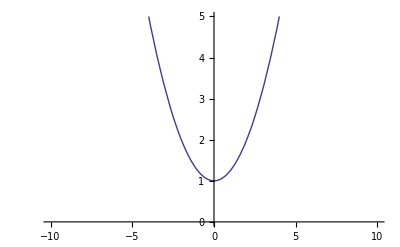

```mathematica
Plot[nu[zs[1]]/.k->.25,{zs[1],-10,10},PlotRange->{0,5}]
```

```mathematica
q
```

q

Export system of equations to C code

```mathematica
recur2c[lhs_,rhs_,variables_,bound_,convergence_]:=Module[{str},
str="";
Assert[Length[lhs]==Length[rhs]];
Assert[Length[lhs]==Length[variables]];

(* first declare rhs *)
For[iter=1,iter≤Length[lhs],iter++,
str=str<>"double "<>tc[lhs[[iter]]]<>";\n\n";
];
(* then iterate *)
str=str<>"for(int iter = 0; iter < 1e08; ++iter) {\n\n";
For[iter=1,iter≤Length[rhs],iter++,
str=str<>tc[lhs[[iter]]]<>" = "<>tc[bound]<>"("<>tc[rhs[[iter]]]<>");\n\n";
];
(* evaluate convergence *)
If[convergence,
str=str<>"if (\n\n";
For[iter=1,iter≤Length[rhs],iter++,
str=str<>"fabs("<>tc[lhs[[iter]]]<>" - "<>tc[variables[[iter]]]<>")<=1e-07";
If[iter<Length[rhs],str=str<>"&&\n\n"];
];
str=str<>")\n\n{break;}\n\n";
];
(* update values *)
For[iter=1,iter≤Length[rhs],iter++,
str=str<>tc[variables[[iter]]]<>" = "<>tc[lhs[[iter]]]<>";\n\n";
];
(* end iteration *)
str =str<>"}\n\n";
(* export to gsl_vector *)
For[iter=1,iter≤Length[rhs],iter++,
str=str<>"gsl_vector_set(f,"<>tc[iter-1]<>","<>tc[variables[[iter]]]<>");\n";
];
Return[str];
]
```

## Patch frequencies

2 players per patch: 2 environments with each individual either adapted or maladapted yielding 2x3 combinations

### Basic functions

```mathematica
patches=Table[f[ei,statex[[1]],statex[[2]]],{ei,1,2},{statex,{{a,a},{a,m},{m,m}}}]//Flatten
```

{f[1,a,a],f[1,a,m],f[1,m,m],f[2,a,a],f[2,a,m],f[2,m,m]}

Determine phenotype of adult living in envt e_i and having state x (a,m)

```mathematica
phen[ei_,state_]:=If[Count[{state},a]>0&&ei==1||Count[{state},m]>0&&ei==2,1,2];
```

Probability p_a(e_1,state_1,state_2) that a locally adapted juvenile occupies a vacant position in a environment e_1-patch previously containing two adult breeders in state1 and state2

```mathematica
pa[ei_,state1_,state2_]:=(1-d)1/2 If[ei==1,p[phen[ei,state1]]+p[phen[ei,state2]],1-p[phen[ei,state1]]+1-p[phen[ei,state2]]]+1/2 d Sum[f[ex,statex[[1]],statex[[2]]]If[ei==1,p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]],
1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]]],{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
pa[1,a,m]/.d->1//FullSimplify
```

1/2 ((2 f[1,a,a]+f[1,a,m]+f[2,a,m]+2 f[2,m,m]) p[1]+(f[1,a,m]+2 (f[1,m,m]+f[2,a,a])+f[2,a,m]) p[2])

```mathematica
pa[1,a,a]/.{d->1,p[1]->1/2,p[2]->1/2}//Simplify
```

1/2 (f[1,a,a]+f[1,a,m]+f[1,m,m]+f[2,a,a]+f[2,a,m]+f[2,m,m])

```mathematica
pa[1,a,a]+pa[1,m,m]+pa[1,a,m]+pa[2,a,m]+pa[2,a,a]+pa[2,m,m]/.d->1/.{p[1]->1/2,p[2]->1/2}
```

3 (f[1,a,a]+f[1,a,m]+f[1,m,m]+f[2,a,a]+f[2,a,m]+f[2,m,m])

### dfaadt - changes in frequency of patches containing two adapted individuals

Environmental change

```mathematica
dfaadt1[ei_]:=Exp[q zs[3-ei,m]]s[3-ei]f[3-ei,m,m]-Exp[q zs[ei,a]]s[ei]f[ei,a,a]
```

Mortality of maladapted individual in f[ei,a,m] patch, replaced by adapted

```mathematica
dfaadt2[ei_]:=mu[m]nu[zs[ei,m]]pa[ei,a,m]f[ei,a,m]
```

Mortality of adapted individual replaced by maladapted

```mathematica
dfaadt3[ei_]:=-2mu[a]nu[zs[ei,a]](1-pa[ei,a,a])f[ei,a,a]
```

```mathematica
dfaadt[ei_]:=dfaadt1[ei]+dfaadt2[ei]+dfaadt3[ei]
```

### dfamdt - changes in frequency of patches containing one adapted and one maladapted breeder

Environmental change

```mathematica
dfamdt1[ei_]:=Exp[q 1/2(zs[3-ei,a]+zs[3-ei,m])]s[3-ei]f[3-ei,a,m]-Exp[q 1/2(zs[ei,a]+zs[ei,m])]s[ei]f[ei,a,m]
```

Mortality of a maladapted individual in a f[ei,m,m] patch, replaced by an adapted individual

```mathematica
dfamdt2[ei_]:=2 mu[m]nu[zs[ei,m]]pa[ei,m,m]f[ei,m,m]
```

Mortality of an adapted individual in a f[ei,a,a] patch, replaced by a maladapted individual

```mathematica
dfamdt3[ei_]:=2 mu[a]nu[zs[ei,a]](1-pa[ei,a,a])f[ei,a,a]
```

Mortality of an adapted individual in a f[e_i,a,m] patch, replaced by a maladapted individual

```mathematica
dfamdt4[ei_]:=-mu[a]nu[zs[ei,a]](1-pa[ei,a,m])f[ei,a,m]
```

Mortality of a maladapted individual in a f[ei,a,m] patch, replaced by an adapted individual

```mathematica
dfamdt5[ei_]:=-mu[m]nu[zs[ei,m]]pa[ei,a,m]f[ei,a,m]
```

Total change:

```mathematica
dfamdt[ei_]:=dfamdt1[ei]+dfamdt2[ei]+dfamdt3[ei]+dfamdt4[ei]+dfamdt5[ei];
```

### dfmmdt - changes in frequency of patches containing two maladapted breeders

```mathematica
dfmmdt1[ei_]:=Exp[q zs[3-ei,m]]s[3-ei]f[3-ei,a,a]-Exp[q zs[ei,m]]s[ei]f[ei,m,m]
```

```mathematica
dfmmdt2[ei_]:=-2mu[m]nu[zs[ei,m]]pa[ei,m,m]f[ei,m,m]
```

```mathematica
dfmmdt3[ei_]:=mu[a]nu[zs[ei,a]](1-pa[ei,a,m])f[ei,a,m]
```

```mathematica
dfmmdt[ei_]:=dfmmdt1[ei]+dfmmdt2[ei]+dfmmdt3[ei]
```

### Solve for equilibrium patch frequencies

Add the constraint that ∑_(i=o)^n p_i=1:

```mathematica
dfdtconst=Total[patches]==1;
```

Generate system of recursion equations:

```mathematica
syspatch=Table[{dfaadt[ei]==0,dfamdt[ei]==0,dfmmdt[ei]==0},{ei,1,2}]//Flatten;
```

```mathematica
patches
```

{f[1,a,a],f[1,a,m],f[1,m,m],f[2,a,a],f[2,a,m],f[2,m,m]}

Make list of recursions, with constraint inserted at different positions. These should result in the same solutions, unless something is wrong:

```mathematica
syspatch1=ReplacePart[syspatch,1->dfdtconst];
syspatch2=ReplacePart[syspatch,6->dfdtconst];
```

Prepare system of recursions for export to C

Numerically solve for testing purposes (solving will be done in C for scalability)

```mathematica
ansTest[{mum_,mua_},{p1_,p2_},{ds_,ks_},{s1_,s2_},{zs1_,zs2_},{qs_}]:=
syspatch1/.{mu[m]->mum,mu[a]->mua,p[1]->p1,p[2]->p2,d->ds,k->ks,s[1]->s1,s[2]->s2,q->qs,zs[1]->zs1,zs[2]->zs2/.f[1,a,a]->1/6,f[1,a,m]->1/6,f[1,m,m]->1/6,f[2,a,a]->1/6,f[2,a,m]->1/6,f[2,m,m]->1/6}
```

```mathematica
ans[{mum_,mua_},{p1_,p2_},{ds_,ks_},{s1_,s2_},{zs1_,zs2_},{qs_}]:=
FindRoot[syspatch1/.{mu[m]->mum,mu[a]->mua,p[1]->p1,p[2]->p2,d->ds,k->ks,s[1]->s1,s[2]->s2,q->qs,zs[1,a]->zs1,zs[2,a]->zs2,zs[1,m]->zs1,zs[2,m]->zs2},{{f[1,a,a],1/6},{f[1,a,m],1/6},{f[1,m,m],1/6},{f[2,a,a],1/6},{f[2,a,m],1/6},{f[2,m,m],1/6}}];
```

```mathematica
ansAlt[{mum_,mua_},{p1_,p2_},{ds_,ks_},{s1_,s2_},{zs1_,zs2_},{qs_}]:=
FindRoot[syspatch2/.{mu[m]->mum,mu[a]->mua,p[1]->p1,p[2]->p2,d->ds,k->ks,s[1]->s1,s[2]->s2,q->qs,zs[1,a]->zs1,zs[2,a]->zs2,zs[1,m]->zs1,zs[2,m]->zs2},{{f[1,a,a],1/6},{f[1,a,m],1/6},{f[1,m,m],1/6},{f[2,a,a],1/6},{f[2,a,m],1/6},{f[2,m,m],1/6}}];
```

```mathematica
ans[{2.0,1.0},{0.5,0.3},{0.2,0},{0.8,0.3},{0,0},{0.5}]
```

{f[1,a,a]→0.0595488,f[1,a,m]→0.117621,f[1,m,m]→0.0955576,f[2,a,a]→0.41431,f[2,a,m]→0.252184,f[2,m,m]→0.0607789}

```mathematica
ansAlt[{2.0,1.0},{0.5,0.3},{0.2,0},{0.8,0.3},{0,0},{0.5}]
```

{f[1,a,a]→0.0595488,f[1,a,m]→0.117621,f[1,m,m]→0.0955576,f[2,a,a]→0.41431,f[2,a,m]→0.252184,f[2,m,m]→0.0607789}

### Export patch frequency equations to C

```mathematica
patchvalstplus1=patches/.f->ftplus1
```

{ftplus1[1,a,a],ftplus1[1,a,m],ftplus1[1,m,m],ftplus1[2,a,a],ftplus1[2,a,m],ftplus1[2,m,m]}

```mathematica
patchsysRHS=Table[{f[ei,a,a]+eul dfaadt[ei],f[ei,a,m]+eul dfamdt[ei],f[ei,m,m]+eul dfmmdt[ei]},{ei,1,2}]/.subslist//Flatten;
patchsysRHS=ReplacePart[patchsysRHS,-1->(f[2,m,m]/.Solve[dfdtconst,f[2,m,m]]/.f->ftplus1)]//Flatten;
```

```mathematica
strpatchFreq=recur2c[patchvalstplus1,patchsysRHS,patches,bound01,True];
```

```mathematica
Export[cdir<>"patchrecurs.txt",strpatchFreq];
```

## Reproductive values

```mathematica
rvals=Table[v[ex,statex1,statex2],{ex,1,2},{statex1,{a,m}},{statex2,{a,m}}]//Flatten;
```

```mathematica
rvalsTest=Table[v[2,statex1,statex2]->v[1,statex1,statex2],
{statex1,{a,m}},{statex2,{a,m}}]//Flatten;
```

### v[e_i,a,m]: Reproductive value of focal adapted individual sharing a environment ei patch with a maladapted individual

Environmental change:

```mathematica
dvamdt1[ei_]:=Exp[q 1/2(zs[ei,a]+zs[ei,m])]s[ei](v[3-ei,m,a]-v[ei,a,m])
```

Mortality of focal, replaced by her own maladapted offspring

```mathematica
dvamdt2[ei_]:=mu[a]nu[zs[ei,a]] 1/2(1-d)If[ei==1,1-p[phen[ei,a]],p[phen[ei,a]]](v[ei,m,m]-v[ei,a,m])
```

Mortality of focal, replaced by nonfocal offspring

```mathematica
dvamdt3[ei_]:=mu[a]nu[zs[ei,a]](1-1/2(1-d))(-v[ei,a,m])
```

Mortality of nonfocal, replaced by focal's offspring

```mathematica
dvamdt4[ei_]:=mu[m]nu[zs[ei,m]] 1/2(1-d)(p[phen[ei,a]]If[ei==1,2v[ei,a,a]-v[ei,a,m],v[ei,m,a]]+(1-p[phen[ei,a]])If[ei==1,v[ei,m,a],2v[ei,a,a]-v[ei,a,m]])
```

Mortality of nonfocal, replaced by nonfocal offspring of a different type than nonfocal

```mathematica
dvamdt5[ei_]:=mu[m]nu[zs[ei,m]](1/2(1-d)If[ei==1,p[phen[ei,m]],1-p[phen[ei,m]]]+1/2 d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]],1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,a,a]-v[ei,a,m])
```

Mortality of individual in remote patch, replaced by focal's offspring

```mathematica
dvamdt6[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,p[phen[ei,a]]v[1,a,statex[[2]]]+(1-p[phen[ei,a]])v[1,m,statex[[2]]],p[phen[ei,a]]v[2,m,statex[[2]]]+(1-p[phen[ei,a]])v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,p[phen[ei,a]]v[1,a,statex[[1]]]+(1-p[phen[ei,a]])v[1,m,statex[[1]]],p[phen[ei,a]]v[2,m,statex[[1]]]+(1-p[phen[ei,a]])v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvamdt[ei_]:=dvamdt1[ei]+dvamdt2[ei]+dvamdt3[ei]+dvamdt4[ei]+dvamdt5[ei]+dvamdt6[ei];
```

### v[e_i,m,a]: Reproductive value of focal maladapted individual sharing a environment ei patch with an adapted individual

Environmental change:

```mathematica
dvmadt1[ei_]:=Exp[q 1/2(zs[ei,m]+zs[ei,a])]s[ei](v[3-ei,a,m]-v[ei,m,a])
```

Mortality of focal, replaced by her own adapted offspring

```mathematica
dvmadt2[ei_]:=mu[m]nu[zs[ei,m]] 1/2(1-d)If[ei==1,p[phen[ei,m]],1-p[phen[ei,m]]](v[ei,a,a]-v[ei,m,a])
```

Mortality of focal, replaced by nonfocal offspring

```mathematica
dvmadt3[ei_]:=mu[m]nu[zs[ei,m]](1-1/2(1-d))(-v[ei,m,a])
```

Mortality of nonfocal, replaced by focal's offspring

```mathematica
dvmadt4[ei_]:=mu[a]nu[zs[ei,a]] 1/2(1-d)(p[phen[ei,m]]If[ei==1,v[ei,a,m],2v[ei,m,m]-v[ei,m,a]]+(1-p[phen[ei,m]])If[ei==1,2v[ei,m,m]-v[ei,m,a],v[ei,a,m]])
```

Mortality of nonfocal adapted, replaced by nonfocal maladapted offspring

```mathematica
dvmadt5[ei_]:=mu[a]nu[zs[ei,a]](1/2(1-d)If[ei==1,1-p[phen[ei,a]],p[phen[ei,a]]]+1/2 d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]],p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,m,m]-v[ei,m,a])
```

Mortality of individual in remote patch, replaced by focal's offspring

```mathematica
dvmadt6[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,p[phen[ei,m]]v[1,a,statex[[2]]]+(1-p[phen[ei,m]])v[1,m,statex[[2]]],p[phen[ei,m]]v[2,m,statex[[2]]]+(1-p[phen[ei,m]])v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,p[phen[ei,m]]v[1,a,statex[[1]]]+(1-p[phen[ei,m]])v[1,m,statex[[1]]],p[phen[ei,m]]v[2,m,statex[[1]]]+(1-p[phen[ei,m]])v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvmadt[ei_]:=dvmadt1[ei]+dvmadt2[ei]+dvmadt3[ei]+dvmadt4[ei]+dvmadt5[ei]+dvmadt6[ei];
```

### v[e_i,a,a] reproductive value of focal adapted individual living in a patch with another adapted individual

Environmental change

```mathematica
dvaadt1[ei_]:=Exp[q zs[ei,a]]s[ei](v[3-ei,m,m]-v[ei,a,a])
```

Focal adapted dies, replaced by her own maladapted offspring

```mathematica
dvaadt2[ei_]:=mu[a]nu[zs[ei,a]] 1/2(1-d)If[ei==1,1-p[phen[ei,a]],p[phen[ei,a]]](v[ei,m,a]-v[ei,a,a])
```

Focal adapted dies, replaced by nonfocal offspring

```mathematica
dvaadt3[ei_]:=mu[a]nu[zs[ei,a]](1-1/2(1-d))(-v[ei,a,a])
```

Nonfocal adapted dies, replaced by focal offspring

```mathematica
dvaadt4[ei_]:=mu[a]nu[zs[ei,a]] 1/2(1-d)If[ei==1,p[phen[ei,a]]v[ei,a,a]+(1-p[phen[ei,a]])(v[ei,m,a]+v[ei,a,m]-v[ei,a,a]),(1-p[phen[ei,a]])v[ei,a,a]+p[phen[ei,a]](v[ei,m,a]+v[ei,a,m]-v[ei,a,a])]
```

Nonfocal adapted dies, replaced by nonfocal maladapted offspring

```mathematica
dvaadt5[ei_]:=mu[a]nu[zs[ei,a]] 1/2((1-d)If[ei==1,1-p[phen[ei,a]],p[phen[ei,a]]]+d*Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]],p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,a,m]-v[ei,a,a])
```

```mathematica
dvaadt6[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,p[phen[ei,a]]v[1,a,statex[[2]]]+(1-p[phen[ei,a]])v[1,m,statex[[2]]],p[phen[ei,a]]v[2,m,statex[[2]]]+(1-p[phen[ei,a]])v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,p[phen[ei,a]]v[1,a,statex[[1]]]+(1-p[phen[ei,a]])v[1,m,statex[[1]]],p[phen[ei,a]]v[2,m,statex[[1]]]+(1-p[phen[ei,a]])v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvaadt[ei_]:=dvaadt1[ei]+dvaadt2[ei]+dvaadt3[ei]+dvaadt4[ei]+dvaadt5[ei]+dvaadt6[ei];
```

### v[e_i,m,m]

Environmental change

```mathematica
dvmmdt1[ei_]:=Exp[q zs[ei,m]]s[ei](v[3-ei,a,a]-v[ei,m,m])
```

Focal dies, replaced by her own adapted offspring

```mathematica
dvmmdt2[ei_]:=mu[m]nu[zs[ei,m]] 1/2(1-d)If[ei==1,p[phen[ei,m]],1-p[phen[ei,m]]](v[ei,a,m]-v[ei,m,m])
```

Focal dies, replaced by nonfocal offspring

```mathematica
dvmmdt3[ei_]:=mu[m]nu[zs[ei,m]](1-1/2(1-d))(-v[ei,m,m])
```

Nonfocal dies, replaced by focal offspring

```mathematica
dvmmdt4[ei_]:=mu[m]nu[zs[ei,m]] 1/2(1-d)If[ei==1,p[phen[ei,m]](v[ei,a,m]+v[ei,m,a]-v[ei,m,m])+(1-p[phen[ei,m]])v[ei,m,m],(1-p[phen[ei,m]])(v[ei,a,m]+v[ei,m,a]-v[ei,m,m])+p[phen[ei,m]]v[ei,m,m]]
```

Nonfocal maladapted dies, replaced by nonfocal adapted offspring

```mathematica
dvmmdt5[ei_]:=mu[m]nu[zs[ei,m]] 1/2((1-d)If[ei==1,p[phen[ei,m]],1-p[phen[ei,m]]]+d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]],1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,m,a]-v[ei,m,m])
```

```mathematica
dvmmdt6[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,p[phen[ei,m]]v[1,a,statex[[2]]]+(1-p[phen[ei,m]])v[1,m,statex[[2]]],p[phen[ei,m]]v[2,m,statex[[2]]]+(1-p[phen[ei,m]])v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,p[phen[ei,m]]v[1,a,statex[[1]]]+(1-p[phen[ei,m]])v[1,m,statex[[1]]],p[phen[ei,m]]v[2,m,statex[[1]]]+(1-p[phen[ei,m]])v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvmmdt[ei_]:=dvmmdt1[ei]+dvmmdt2[ei]+dvmmdt3[ei]+dvmmdt4[ei]+dvmmdt5[ei]+dvmmdt6[ei];
```

### Find equilibrium reproductive values

```mathematica
rvsys=Table[{dvmmdt[ei]==0,dvaadt[ei]==0,dvamdt[ei]==0,dvmadt[ei]==0},{ei,1,2}]//Flatten;
```

```mathematica
rvconstraint=Sum[f[ei,a,a]v[ei,a,a]+f[ei,m,m]v[ei,m,m]+1/2 f[ei,a,m](v[ei,a,m]+v[ei,m,a]),{ei,1,2}]==1;
```

```mathematica
rvconstraint
```

f[1,a,a] v[1,a,a]+1/2 f[1,a,m] (v[1,a,m]+v[1,m,a])+f[1,m,m] v[1,m,m]+f[2,a,a] v[2,a,a]+1/2 f[2,a,m] (v[2,a,m]+v[2,m,a])+f[2,m,m] v[2,m,m]==1

```mathematica
rvsys1=ReplacePart[rvsys,1->rvconstraint];
rvsys2=ReplacePart[rvsys,5->rvconstraint];
rvinit=Table[{rvali,1},{rvali,rvals}];
rvinittest=Table[rvali->1,{rvali,rvals}]
```

{v[1,a,a]→1,v[1,a,m]→1,v[1,m,a]→1,v[1,m,m]→1,v[2,a,a]→1,v[2,a,m]→1,v[2,m,a]→1,v[2,m,m]→1}

```mathematica
ansRVtest[{mum_,mua_},{p1_,p2_},{ds_,ks_},{s1_,s2_},{zs1_,zs2_},{qs_}]:=
rvsys1/.{mu[m]->mum,mu[a]->mua,p[1]->p1,p[2]->p2,d->ds,k->ks,s[1]->s1,s[2]->s2,q->qs,zs[1,a]->zs1,zs[2,a]->zs2,zs[1,m]->zs1,zs[2,m]->zs2}/.ans[{mum,mua},{p1,p2},{ds,ks},{s1,s2},{zs1,zs2},{qs}]/.rvinittest
```

```mathematica
ansRV[{mum_,mua_},{p1_,p2_},{ds_,ks_},{s1_,s2_},{zs1_,zs2_},{qs_}]:=
FindRoot[rvsys1/.{mu[m]->mum,mu[a]->mua,p[1]->p1,p[2]->p2,d->ds,k->ks,s[1]->s1,s[2]->s2,q->qs,zs[1,a]->zs1,zs[2,a]->zs2,zs[1,m]->zs1,zs[2,m]->zs2}/.ans[{mum,mua},{p1,p2},{ds,ks},{s1,s2},{zs1,zs2},{qs}],rvinit]
```

```mathematica
ansRValt[{mum_,mua_},{p1_,p2_},{ds_,ks_},{s1_,s2_},{zs1_,zs2_},{qs_}]:=
FindRoot[rvsys2/.{mu[m]->mum,mu[a]->mua,p[1]->p1,p[2]->p2,d->ds,k->ks,q->qs,s[1]->s1,s[2]->s2,zs[1,a]->zs1,zs[2,a]->zs2,zs[1,m]->zs1,zs[2,m]->zs2}/.ans[{mum,mua},{p1,p2},{ds,ks},{s1,s2},{zs1,zs2},{qs}],rvinit]
```

```mathematica
ansRVtest[{2.0,1.0},{0.5,0.3},{0.2,0.8},{0.8,0.3},{0.9,1.1},{0.5}]
```

{True,False,False,False,False,False,False,False}

```mathematica
ansRV[{2.0,1.0},{0.5,0.3},{0.2,0},{0.8,0.3},{0,0},{0.5}]
ansRValt[{2.0,1.0},{0.2,0.5},{0.5,0},{0.25,0.5},{1.3,1.0},{0.5}]
```

{v[1,a,a]→0.981876,v[1,a,m]→1.07624,v[1,m,a]→0.848367,v[1,m,m]→0.933169,v[2,a,a]→1.0497,v[2,a,m]→1.19799,v[2,m,a]→0.775888,v[2,m,m]→0.911153}

{v[1,a,a]→1.09237,v[1,a,m]→1.16444,v[1,m,a]→0.817765,v[1,m,m]→0.883749,v[2,a,a]→1.06881,v[2,a,m]→1.12571,v[2,m,a]→0.867925,v[2,m,m]→0.919883}

### Export reproductive value equations to C

```mathematica
rvsysRHS=Table[{v[ei,a,a]+eul * dvaadt[ei],v[ei,a,m]+eul * dvamdt[ei],v[ei,m,a]+eul*dvmadt[ei],v[ei,m,m]+eul*dvmmdt[ei]},{ei,1,2}]/.subslist//Flatten;
```

```mathematica
rvalstplus1=rvals/.v->vtplus1;
```

Add constraint to system of equations, by means of v_(t+1)[2,m,m]=something.

```mathematica
rvsysRHS=ReplacePart[rvsysRHS,-1->((v[2,m,m]/.Solve[rvconstraint,v[2,m,m]])/.v->vtplus1)]//Flatten;
```

```mathematica
strRVfreq=recur2c[rvalstplus1,rvsysRHS,rvals,bound0,True];
```

```mathematica
Export[cdir<>"repvals.txt",strRVfreq];
```

## Relatedness

### Relatedness between two adapted breeders in environment ei

Environmental change

```mathematica
draadt1[ei_]:=f[3-ei,m,m]Exp[q zs[3-ei,m]]s[3-ei]rmm[3-ei]
draadt1dn[ei_]:=f[3-ei,m,m]Exp[q zs[3-ei,m]]s[3-ei]
```

Mortality adapted breeder on aa patch, replaced by adapted individual

```mathematica
draadt2[ei_]:=2f[ei,a,a]mu[a]nu[zs[ei,a]](1-d)If[ei==1,p[1],1-p[2]] 1/2(1+raa[ei])
draadt2dn[ei_]:=2f[ei,a,a]mu[a]nu[zs[ei,a]]pa[ei,a,a]
```

Mortality maladapted breeder on a am patch, replaced by an adapted one

```mathematica
draadt3[ei_]:=f[ei,a,m]mu[m]nu[zs[ei,m]](1-d)If[ei==1,1/2 p[1]+1/2 p[2]ram[ei],1/2(1-p[2])+1/2(1-p[1])ram[ei]]
draadt3dn[ei_]:=f[ei,a,m]mu[m]nu[zs[ei,m]]pa[ei,a,m]
```

```mathematica
draadt[ei_]:=(draadt1[ei]+draadt2[ei]+draadt3[ei])/(draadt1dn[ei]+draadt2dn[ei]+draadt3dn[ei])
```

### Relatedness between adapted and maladapted breeder in environment ei

Environmental change

```mathematica
dramdt1[ei_]:=f[3-ei,a,m]s[3-ei]Exp[q 1/2(zs[3-ei,m]+zs[3-ei,a])]ram[3-ei]
dramdt1dn[ei_]:=f[3-ei,a,m]s[3-ei]Exp[q 1/2(zs[3-ei,m]+zs[3-ei,a])]
```

Mortality maladapted breeder on mm patch, replaced by adapted breeder

```mathematica
dramdt2[ei_]:=2f[ei,m,m]mu[m]nu[zs[ei,m]](1-d)If[ei==1,p[2],(1-p[1])] 1/2(1+rmm[ei])
dramdt2dn[ei_]:=2f[ei,m,m]mu[m]nu[zs[ei,m]]pa[ei,m,m]
```

Mortality adapted breeder on aa patch, replaced by maladapted breeder

```mathematica
dramdt3[ei_]:=2 f[ei,a,a]mu[a]nu[zs[ei,a]](1-d)If[ei==1,1-p[1],p[2]] 1/2(1+raa[ei])
dramdt3dn[ei_]:=2 f[ei,a,a]mu[a]nu[zs[ei,a]](1-pa[ei,a,a])
```

Mortality maladapted breeder on am patch, replaced by maladapted breeder

```mathematica
dramdt4[ei_]:=f[ei,a,m]mu[m]nu[zs[ei,m]](1-d)If[ei==1,1/2(1-p[1])+1/2(1-p[2])ram[ei],1/2 p[1]ram[ei]+1/2 p[2]]
dramdt4dn[ei_]:=f[ei,a,m]mu[m]nu[zs[ei,m]](1-pa[ei,a,m])
```

Mortality adapted breeder on am patch, replaced by adapted breeder

```mathematica
dramdt5[ei_]:=f[ei,a,m]mu[a]nu[zs[ei,a]](1-d)If[ei==1,1/2 p[1]ram[ei]+1/2 p[2],1/2(1-p[1])+1/2(1-p[2])ram[ei]]
dramdt5dn[ei_]:=f[ei,a,m]mu[a]nu[zs[ei,a]]pa[ei,a,m]
```

```mathematica
dramdt[ei_]:=(dramdt1[ei]+dramdt2[ei]+dramdt3[ei]+dramdt4[ei]+dramdt5[ei])/(dramdt1dn[ei]+dramdt2dn[ei]+dramdt3dn[ei]+dramdt4dn[ei]+dramdt5dn[ei])
```

### Relatedness between maladapted breeders in environment ei

Environmental change

```mathematica
drmmdt1[ei_]:=f[3-ei,a,a]s[3-ei]Exp[q zs[3-ei,a]]raa[3-ei]
drmmdt1dn[ei_]:=f[3-ei,a,a]s[3-ei]Exp[q zs[3-ei,a]]
```

Mortality adapted breeder on a am patch, replaced by maladapted breeder

```mathematica
drmmdt2[ei_]:=f[ei,a,m]mu[a]nu[zs[ei,a]] 1/2(1-d)If[ei==1,(1-p[1])ram[ei]+(1-p[2]),p[1]+p[2]ram[ei]]
drmmdt2dn[ei_]:=f[ei,a,m]mu[a]nu[zs[ei,a]](1-pa[ei,a,m])
```

Mortality maladapted breeder on a mm patch, replaced by maladapted breeder

```mathematica
drmmdt3[ei_]:=2f[ei,m,m]mu[m]nu[zs[ei,m]](1-d)If[ei==1,(1-p[2]),p[1]] 1/2(1+rmm[ei])
drmmdt3dn[ei_]:=2f[ei,m,m]mu[m]nu[zs[ei,m]](1-pa[ei,m,m])
```

```mathematica
drmmdt[ei_]:=(drmmdt1[ei]+drmmdt2[ei]+drmmdt3[ei])/(drmmdt1dn[ei]+drmmdt2dn[ei]+drmmdt3dn[ei])
```

### Numerical solutions

```mathematica
relsys=Table[{draadt[ei]==raa[ei],dramdt[ei]==ram[ei],drmmdt[ei]==rmm[ei]},{ei,1,2}]//Flatten;
```

```mathematica
ansrel[{mum_,mua_},{p1_,p2_},{ds_,ks_},{s1_,s2_},{zs1_,zs2_},{qs_}]:=
FindRoot[relsys/.{mu[m]->mum,mu[a]->mua,p[1]->p1,p[2]->p2,d->ds,k->ks,s[1]->s1,s[2]->s2,q->qs,zs[1,a]->zs1,zs[2,a]->zs2,zs[1,m]->zs1,zs[2,m]->zs2}/.ans[{mum,mua},{p1,p2},{ds,ks},{s1,s2},{zs1,zs2},{qs}],{{rmm[1],0.1},{rmm[2],0.1},{ram[1],0.1},{ram[2],0.1},{raa[1],0.1},{raa[2],0.1}}]
```

```mathematica
ansrel[{2.0,1.0},{0.0001,0.0001},{0.2,0},{20,0.001},{6,-6},{0.5}]
```

{rmm[1]→0.666667,rmm[2]→0.666667,ram[1]→0.666667,ram[2]→0.666667,raa[1]→0.666667,raa[2]→0.666667}

### Export relatedness equations to C

```mathematica
relvals=Table[{raa[ei],ram[ei],rmm[ei]},{ei,1,2}]//Flatten;
relvalstplus1=Flatten[Table[{raatplus1[ei],ramtplus1[ei],rmmtplus1[ei]},{ei,1,2}]];
```

```mathematica
relRHS=Table[{draadt[ei], dramdt[ei],drmmdt[ei]},{ei,1,2}]/.subslist//Flatten;
```

```mathematica
strrel=recur2c[relvalstplus1,relRHS,relvals,bound01,True];
```

```mathematica
Export[cdir<>"relvals.txt",strrel];
```

## Selection gradient p1, p2

```mathematica
rvals=Table[v[ex,statex1,statex2],{ex,1,2},{statex1,{a,m}},{statex2,{a,m}}]//Flatten;
```

```mathematica
rvalsTest=Table[v[2,statex1,statex2]->v[1,statex1,statex2],
{statex1,{a,m}},{statex2,{a,m}}]//Flatten;
```

### dv[e_i,a,m]/dδp

Environmental change:

```mathematica
dvamdt1δp[ei_]:=Exp[q 1/2(zs[ei,a]+zs[ei,m])]s[ei](v[3-ei,m,a]-v[ei,a,m])
```

Mortality of focal, replaced by her own maladapted offspring

```mathematica
dvamdt2δp[ei_]:=mu[a]nu[zs[ei,a]] 1/2(1-d)If[ei==1,1-(p[phen[ei,a]]+δp[phen[ei,a]]),(p[phen[ei,a]]+δp[phen[ei,a]])](v[ei,m,m]-v[ei,a,m])
```

Mortality of focal, replaced by nonfocal offspring

```mathematica
dvamdt3δp[ei_]:=mu[a]nu[zs[ei,a]](1-1/2(1-d))(-v[ei,a,m])
```

Mortality of nonfocal, replaced by focal's offspring

```mathematica
dvamdt4δp[ei_]:=mu[m]nu[zs[ei,m]] 1/2(1-d)((p[phen[ei,a]]+δp[phen[ei,a]])If[ei==1,2v[ei,a,a]-v[ei,a,m],v[ei,m,a]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))If[ei==1,v[ei,m,a],2v[ei,a,a]-v[ei,a,m]])
```

Mortality of nonfocal, replaced by nonfocal offspring of a different type than nonfocal

```mathematica
dvamdt5δp[ei_]:=mu[m]nu[zs[ei,m]](1/2(1-d)If[ei==1,(p[phen[ei,m]]+ram[ei]δp[phen[ei,m]]),1-(p[phen[ei,m]]+ram[ei]δp[phen[ei,m]])]+1/2 d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]],1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,a,a]-v[ei,a,m])
```

Mortality of individual in remote patch, replaced by focal's offspring

```mathematica
dvamdt6δp[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,(p[phen[ei,a]]+δp[phen[ei,a]])v[1,a,statex[[2]]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[1,m,statex[[2]]],(p[phen[ei,a]]+δp[phen[ei,a]])v[2,m,statex[[2]]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,(p[phen[ei,a]]+δp[phen[ei,a]])v[1,a,statex[[1]]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[1,m,statex[[1]]],(p[phen[ei,a]]+δp[phen[ei,a]])v[2,m,statex[[1]]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvamdtδp[ei_]:=dvamdt1δp[ei]+dvamdt2δp[ei]+dvamdt3δp[ei]+dvamdt4δp[ei]+dvamdt5δp[ei]+dvamdt6δp[ei];
```

### dv[e_i,m,a]/dδp

Environmental change:

```mathematica
dvmadt1δp[ei_]:=Exp[q 1/2(zs[ei,m]+zs[ei,a])]s[ei](v[3-ei,a,m]-v[ei,m,a])
```

Mortality of focal, replaced by her own adapted offspring

```mathematica
dvmadt2δp[ei_]:=mu[m]nu[zs[ei,m]] 1/2(1-d)If[ei==1,p[phen[ei,m]]+δp[phen[ei,m]],1-p[phen[ei,m]]-δp[phen[ei,m]]](v[ei,a,a]-v[ei,m,a])
```

Mortality of focal, replaced by nonfocal offspring

```mathematica
dvmadt3δp[ei_]:=mu[m]nu[zs[ei,m]](1-1/2(1-d))(-v[ei,m,a])
```

Mortality of nonfocal, replaced by focal's offspring

```mathematica
dvmadt4δp[ei_]:=mu[a]nu[zs[ei,a]] 1/2(1-d)((p[phen[ei,m]]+δp[phen[ei,m]])If[ei==1,v[ei,a,m],2v[ei,m,m]-v[ei,m,a]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))If[ei==1,2v[ei,m,m]-v[ei,m,a],v[ei,a,m]])
```

Mortality of nonfocal adapted, replaced by nonfocal maladapted offspring

```mathematica
dvmadt5δp[ei_]:=mu[a]nu[zs[ei,a]](1/2(1-d)If[ei==1,1-(p[phen[ei,a]]+ram[ei] δp[phen[ei,a]]),(p[phen[ei,a]]+ram[ei] δp[phen[ei,a]])]+1/2 d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]],p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,m,m]-v[ei,m,a])
```

Mortality of individual in remote patch, replaced by focal's offspring

```mathematica
dvmadt6δp[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,(p[phen[ei,m]]+δp[phen[ei,m]])v[1,a,statex[[2]]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[1,m,statex[[2]]],(p[phen[ei,m]]+δp[phen[ei,m]])v[2,m,statex[[2]]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,(p[phen[ei,m]]+δp[phen[ei,m]])v[1,a,statex[[1]]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[1,m,statex[[1]]],(p[phen[ei,m]]+δp[phen[ei,m]])v[2,m,statex[[1]]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvmadtδp[ei_]:=dvmadt1δp[ei]+dvmadt2δp[ei]+dvmadt3δp[ei]+dvmadt4δp[ei]+dvmadt5δp[ei]+dvmadt6δp[ei];
```

### dv[e_i,a,a]/dδp

Environmental change

```mathematica
dvaadt1δp[ei_]:=Exp[q zs[ei,a]]s[ei](v[3-ei,m,m]-v[ei,a,a])
```

Focal adapted dies, replaced by her own maladapted offspring

```mathematica
dvaadt2δp[ei_]:=mu[a]nu[zs[ei,a]] 1/2(1-d)If[ei==1,1-(p[phen[ei,a]]+δp[phen[ei,a]]),p[phen[ei,a]]+δp[phen[ei,a]]](v[ei,m,a]-v[ei,a,a])
```

Focal adapted dies, replaced by nonfocal offspring

```mathematica
dvaadt3δp[ei_]:=mu[a]nu[zs[ei,a]](1-1/2(1-d))(-v[ei,a,a])
```

Nonfocal adapted dies, replaced by focal offspring

```mathematica
dvaadt4δp[ei_]:=mu[a]nu[zs[ei,a]] 1/2(1-d)If[ei==1,(p[phen[ei,a]]+δp[phen[ei,a]])v[ei,a,a]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))(v[ei,m,a]+v[ei,a,m]-v[ei,a,a]),(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[ei,a,a]+(p[phen[ei,a]]+δp[phen[ei,a]])(v[ei,m,a]+v[ei,a,m]-v[ei,a,a])]
```

Nonfocal adapted dies, replaced by nonfocal maladapted offspring

```mathematica
dvaadt5δp[ei_]:=mu[a]nu[zs[ei,a]] 1/2((1-d)If[ei==1,1-(p[phen[ei,a]]+raa[ei]δp[phen[ei,a]]),(p[phen[ei,a]]+raa[ei]δp[phen[ei,a]])]+d*Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]],p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,a,m]-v[ei,a,a])
```

```mathematica
dvaadt6δp[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,(p[phen[ei,a]]+δp[phen[ei,a]])v[1,a,statex[[2]]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[1,m,statex[[2]]],(p[phen[ei,a]]+δp[phen[ei,a]])v[2,m,statex[[2]]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,(p[phen[ei,a]]+δp[phen[ei,a]])v[1,a,statex[[1]]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[1,m,statex[[1]]],(p[phen[ei,a]]+δp[phen[ei,a]])v[2,m,statex[[1]]]+(1-(p[phen[ei,a]]+δp[phen[ei,a]]))v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvaadtδp[ei_]:=dvaadt1δp[ei]+dvaadt2δp[ei]+dvaadt3δp[ei]+dvaadt4δp[ei]+dvaadt5δp[ei]+dvaadt6δp[ei];
```

### dv[e_i,m,m]/dδp

Environmental change

```mathematica
dvmmdt1δp[ei_]:=Exp[q zs[ei,m]]s[ei](v[3-ei,a,a]-v[ei,m,m])
```

Focal dies, replaced by her own adapted offspring

```mathematica
dvmmdt2δp[ei_]:=mu[m]nu[zs[ei,m]] 1/2(1-d)If[ei==1,(p[phen[ei,m]]+δp[phen[ei,m]]),1-(p[phen[ei,m]]+δp[phen[ei,m]])](v[ei,a,m]-v[ei,m,m])
```

Focal dies, replaced by nonfocal offspring

```mathematica
dvmmdt3δp[ei_]:=mu[m]nu[zs[ei,m]](1-1/2(1-d))(-v[ei,m,m])
```

Nonfocal dies, replaced by focal offspring

```mathematica
dvmmdt4δp[ei_]:=mu[m]nu[zs[ei,m]] 1/2(1-d)If[ei==1,(p[phen[ei,m]]+δp[phen[ei,m]])(v[ei,a,m]+v[ei,m,a]-v[ei,m,m])+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[ei,m,m],(1-(p[phen[ei,m]]+δp[phen[ei,m]]))(v[ei,a,m]+v[ei,m,a]-v[ei,m,m])+(p[phen[ei,m]]+δp[phen[ei,m]])v[ei,m,m]]
```

Nonfocal maladapted dies, replaced by nonfocal adapted offspring

```mathematica
dvmmdt5δp[ei_]:=mu[m]nu[zs[ei,m]] 1/2((1-d)If[ei==1,(p[phen[ei,m]]+rmm[ei]δp[phen[ei,m]]),1-(p[phen[ei,m]]+rmm[ei]δp[phen[ei,m]])]+d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]],1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,m,a]-v[ei,m,m])
```

```mathematica
dvmmdt6δp[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,(p[phen[ei,m]]+δp[phen[ei,m]])v[1,a,statex[[2]]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[1,m,statex[[2]]],(p[phen[ei,m]]+δp[phen[ei,m]])v[2,m,statex[[2]]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,(p[phen[ei,m]]+δp[phen[ei,m]])v[1,a,statex[[1]]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[1,m,statex[[1]]],(p[phen[ei,m]]+δp[phen[ei,m]])v[2,m,statex[[1]]]+(1-(p[phen[ei,m]]+δp[phen[ei,m]]))v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvmmdtδp[ei_]:=dvmmdt1δp[ei]+dvmmdt2δp[ei]+dvmmdt3δp[ei]+dvmmdt4δp[ei]+dvmmdt5δp[ei]+dvmmdt6δp[ei];
```

```mathematica
selgrad[x_]:=D[Sum[2 f[ei,a,a]dvaadtδp[ei]+f[ei,a,m]dvamdtδp[ei]+f[ei,a,m]dvmadtδp[ei]+2f[ei,m,m]dvmmdtδp[ei],{ei,1,2}],x]
```

## Selection gradient zs1, zs2

```mathematica
rvals=Table[v[ex,statex1,statex2],{ex,1,2},{statex1,{a,m}},{statex2,{a,m}}]//Flatten;
```

```mathematica
rvalsTest=Table[v[2,statex1,statex2]->v[1,statex1,statex2],
{statex1,{a,m}},{statex2,{a,m}}]//Flatten;
```

### dv[e_i,a,m]/dδz

Environmental change:

```mathematica
dvamdt1δz[ei_]:=Exp[q 1/2(zs[ei,a]+δzs[ei,a]+zs[ei,m]+ram[ei]δzs[ei,m])]s[ei](v[3-ei,m,a]-v[ei,a,m])
```

Mortality of focal, replaced by her own maladapted offspring

```mathematica
dvamdt2δz[ei_]:=mu[a]nu[zs[ei,a]+δzs[ei,a]] 1/2(1-d)If[ei==1,1-p[phen[ei,a]],p[phen[ei,a]]](v[ei,m,m]-v[ei,a,m])
```

Mortality of focal, replaced by nonfocal offspring

```mathematica
dvamdt3δz[ei_]:=mu[a]nu[zs[ei,a]+δzs[ei,a]](1-1/2(1-d))(-v[ei,a,m])
```

Mortality of nonfocal, replaced by focal's offspring

```mathematica
dvamdt4δz[ei_]:=mu[m]nu[zs[ei,m]+ram[ei] δzs[ei,m]] 1/2(1-d)(p[phen[ei,a]]If[ei==1,2v[ei,a,a]-v[ei,a,m],v[ei,m,a]]+(1-p[phen[ei,a]])If[ei==1,v[ei,m,a],2v[ei,a,a]-v[ei,a,m]])
```

Mortality of nonfocal, replaced by nonfocal offspring of a different type than nonfocal

```mathematica
dvamdt5δz[ei_]:=mu[m]nu[zs[ei,m]+ram[ei] δzs[ei,m]](1/2(1-d)If[ei==1,p[phen[ei,m]],1-p[phen[ei,m]]]+1/2 d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]],1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,a,a]-v[ei,a,m])
```

Mortality of individual in remote patch, replaced by focal's offspring

```mathematica
dvamdt6δz[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,p[phen[ei,a]]v[1,a,statex[[2]]]+(1-p[phen[ei,a]])v[1,m,statex[[2]]],p[phen[ei,a]]v[2,m,statex[[2]]]+(1-p[phen[ei,a]])v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,p[phen[ei,a]]v[1,a,statex[[1]]]+(1-p[phen[ei,a]])v[1,m,statex[[1]]],p[phen[ei,a]]v[2,m,statex[[1]]]+(1-p[phen[ei,a]])v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvamdtδz[ei_]:=dvamdt1δz[ei]+dvamdt2δz[ei]+dvamdt3δz[ei]+dvamdt4δz[ei]+dvamdt5δz[ei]+dvamdt6δz[ei];
```

```mathematica
D[dvamdtδz[1],δzs[1,a]]
```

1/2 ⅇ^(1/2 q (zs[1,a]+zs[1,m]+δzs[1,a]+ram[1] δzs[1,m])) q s[1] (-v[1,a,m]+v[2,m,a])-2 (1+1/2 (-1+d)) k mu[a] v[1,a,m] (zs[1,a]+δzs[1,a])+(1-d) k mu[a] (1-p[1]) (-v[1,a,m]+v[1,m,m]) (zs[1,a]+δzs[1,a])

### dv[e_i,m,a]/dδz

Environmental change:

```mathematica
dvmadt1δz[ei_]:=Exp[q 1/2(zs[ei,m]+δzs[ei,m]+zs[ei,a]+ram[ei]δzs[ei,a])]s[ei](v[3-ei,a,m]-v[ei,m,a])
```

Mortality of focal, replaced by her own adapted offspring

```mathematica
dvmadt2δz[ei_]:=mu[m]nu[zs[ei,m]+δzs[ei,m]] 1/2(1-d)If[ei==1,p[phen[ei,m]],1-p[phen[ei,m]]](v[ei,a,a]-v[ei,m,a])
```

Mortality of focal, replaced by nonfocal offspring

```mathematica
dvmadt3δz[ei_]:=mu[m]nu[zs[ei,m]+δzs[ei,m]](1-1/2(1-d))(-v[ei,m,a])
```

Mortality of nonfocal, replaced by focal's offspring

```mathematica
dvmadt4δz[ei_]:=mu[a]nu[zs[ei,a]+ram[ei]δzs[ei,a]] 1/2(1-d)(p[phen[ei,m]]If[ei==1,v[ei,a,m],2v[ei,m,m]-v[ei,m,a]]+(1-p[phen[ei,m]])If[ei==1,2v[ei,m,m]-v[ei,m,a],v[ei,a,m]])
```

Mortality of nonfocal adapted, replaced by nonfocal maladapted offspring

```mathematica
dvmadt5δz[ei_]:=mu[a]nu[zs[ei,a]+ram[ei]δzs[ei,a]](1/2(1-d)If[ei==1,1-p[phen[ei,a]],p[phen[ei,a]]]+1/2 d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]],p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,m,m]-v[ei,m,a])
```

Mortality of individual in remote patch, replaced by focal's offspring

```mathematica
dvmadt6δz[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,p[phen[ei,m]]v[1,a,statex[[2]]]+(1-p[phen[ei,m]])v[1,m,statex[[2]]],p[phen[ei,m]]v[2,m,statex[[2]]]+(1-p[phen[ei,m]])v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,p[phen[ei,m]]v[1,a,statex[[1]]]+(1-p[phen[ei,m]])v[1,m,statex[[1]]],p[phen[ei,m]]v[2,m,statex[[1]]]+(1-p[phen[ei,m]])v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvmadtδz[ei_]:=dvmadt1δz[ei]+dvmadt2δz[ei]+dvmadt3δz[ei]+dvmadt4δz[ei]+dvmadt5δz[ei]+dvmadt6δz[ei];
```

### dv[e_i,a,a]/dδz

Environmental change

```mathematica
dvaadt1δz[ei_]:=Exp[q 1/2(zs[ei,a]+δzs[ei,a]+zs[ei,a]+raa[ei]δzs[ei,a])]s[ei](v[3-ei,m,m]-v[ei,a,a])
```

Focal adapted dies, replaced by her own maladapted offspring

```mathematica
dvaadt2δz[ei_]:=mu[a]nu[zs[ei,a]+δzs[ei,a]] 1/2(1-d)If[ei==1,1-p[phen[ei,a]],p[phen[ei,a]]](v[ei,m,a]-v[ei,a,a])
```

Focal adapted dies, replaced by nonfocal offspring

```mathematica
dvaadt3δz[ei_]:=mu[a]nu[zs[ei,a]+δzs[ei,a]](1-1/2(1-d))(-v[ei,a,a])
```

Nonfocal adapted dies, replaced by focal offspring

```mathematica
dvaadt4δz[ei_]:=mu[a]nu[zs[ei,a]+raa[ei]δzs[ei,a]] 1/2(1-d)If[ei==1,p[phen[ei,a]]v[ei,a,a]+(1-p[phen[ei,a]])(v[ei,m,a]+v[ei,a,m]-v[ei,a,a]),(1-p[phen[ei,a]])v[ei,a,a]+p[phen[ei,a]](v[ei,m,a]+v[ei,a,m]-v[ei,a,a])]
```

Nonfocal adapted dies, replaced by nonfocal maladapted offspring

```mathematica
dvaadt5δz[ei_]:=mu[a]nu[zs[ei,a]+raa[ei]δzs[ei,a]] 1/2((1-d)If[ei==1,1-p[phen[ei,a]],p[phen[ei,a]]]+d*Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]],p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,a,m]-v[ei,a,a])
```

```mathematica
dvaadt6δz[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,p[phen[ei,a]]v[1,a,statex[[2]]]+(1-p[phen[ei,a]])v[1,m,statex[[2]]],p[phen[ei,a]]v[2,m,statex[[2]]]+(1-p[phen[ei,a]])v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,p[phen[ei,a]]v[1,a,statex[[1]]]+(1-p[phen[ei,a]])v[1,m,statex[[1]]],p[phen[ei,a]]v[2,m,statex[[1]]]+(1-p[phen[ei,a]])v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvaadtδz[ei_]:=dvaadt1δz[ei]+dvaadt2δz[ei]+dvaadt3δz[ei]+dvaadt4δz[ei]+dvaadt5δz[ei]+dvaadt6δz[ei];
```

### dv[e_i,m,m]/dδz

Environmental change

```mathematica
dvmmdt1δz[ei_]:=Exp[q 1/2(zs[ei,m]+δzs[ei,m]+zs[ei,m]+rmm[ei]δzs[ei,m])]s[ei](v[3-ei,a,a]-v[ei,m,m])
```

Focal dies, replaced by her own adapted offspring

```mathematica
dvmmdt2δz[ei_]:=mu[m]nu[zs[ei,m]+δzs[ei,m]] 1/2(1-d)If[ei==1,p[phen[ei,m]],1-p[phen[ei,m]]](v[ei,a,m]-v[ei,m,m])
```

Focal dies, replaced by nonfocal offspring

```mathematica
dvmmdt3δz[ei_]:=mu[m]nu[zs[ei,m]+δzs[ei,m]](1-1/2(1-d))(-v[ei,m,m])
```

Nonfocal dies, replaced by focal offspring

```mathematica
dvmmdt4δz[ei_]:=mu[m]nu[zs[ei,m]+rmm[ei]δzs[ei,m]] 1/2(1-d)If[ei==1,p[phen[ei,m]](v[ei,a,m]+v[ei,m,a]-v[ei,m,m])+(1-p[phen[ei,m]])v[ei,m,m],(1-p[phen[ei,m]])(v[ei,a,m]+v[ei,m,a]-v[ei,m,m])+p[phen[ei,m]]v[ei,m,m]]
```

Nonfocal maladapted dies, replaced by nonfocal adapted offspring

```mathematica
dvmmdt5δz[ei_]:=mu[m]nu[zs[ei,m]+rmm[ei]δzs[ei,m]] 1/2((1-d)If[ei==1,p[phen[ei,m]],1-p[phen[ei,m]]]+d Sum[f[ex,statex[[1]],statex[[2]]](If[ei==1,p[phen[ex,statex[[1]]]]+p[phen[ex,statex[[2]]]],1-p[phen[ex,statex[[1]]]]+1-p[phen[ex,statex[[2]]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}])(v[ei,m,a]-v[ei,m,m])
```

```mathematica
dvmmdt6δz[ei_]:=1/2 d Sum[f[ex,statex[[1]],statex[[2]]](mu[statex[[1]]]nu[zs[ex,statex[[1]]]]If[ex==1,p[phen[ei,m]]v[1,a,statex[[2]]]+(1-p[phen[ei,m]])v[1,m,statex[[2]]],p[phen[ei,m]]v[2,m,statex[[2]]]+(1-p[phen[ei,m]])v[2,a,statex[[2]]]]+mu[statex[[2]]]nu[zs[ex,statex[[2]]]]If[ex==1,p[phen[ei,m]]v[1,a,statex[[1]]]+(1-p[phen[ei,m]])v[1,m,statex[[1]]],p[phen[ei,m]]v[2,m,statex[[1]]]+(1-p[phen[ei,m]])v[2,a,statex[[1]]]]),{ex,1,2},{statex,{{a,a},{a,m},{m,m}}}]
```

```mathematica
dvmmdtδz[ei_]:=dvmmdt1δz[ei]+dvmmdt2δz[ei]+dvmmdt3δz[ei]+dvmmdt4δz[ei]+dvmmdt5δz[ei]+dvmmdt6δz[ei];
```

```mathematica
selgradδz[x_]:=D[Sum[2 f[ei,a,a]dvaadtδz[ei]+f[ei,a,m]dvamdtδz[ei]+f[ei,a,m]dvmadtδz[ei]+2f[ei,m,m]dvmmdtδz[ei],{ei,1,2}],x]
```

```mathematica
dze1=selgradδz[δzs[1,m]]+selgradδz[δzs[1,a]]/.{δzs[1,m]->0,δzs[1,a]->0};
dze2=selgradδz[δzs[2,m]]+selgradδz[δzs[2,a]]/.{δzs[2,m]->0,δzs[2,a]->0};
```

### Export selection gradients to C

```mathematica
strselgrads="";
strselgrads=strselgrads<>"double p1tplus1 = bound01(p1 + eul * ("<>tc[selgrad[δp[1]]/.subslist]<>"));\n\n";
strselgrads=strselgrads<>"double p2tplus1 = bound01(p2 + eul * ("<>tc[selgrad[δp[2]]/.subslist]<>"));\n\n";
strselgrads=strselgrads<>"double zs1tplus1 = zs1 + eul * ("<>tc[dze1/.subslist]<>");\n\n";
strselgrads=strselgrads<>"double zs2tplus1 = zs2 + eul * ("<>tc[dze2/.subslist]<>");\n\n";
strselgrads=strselgrads<>"gsl_vector_set(f, 0, p1tplus1);\n";
strselgrads=strselgrads<>"gsl_vector_set(f, 1, p2tplus1);\n";
strselgrads=strselgrads<>"gsl_vector_set(f, 2, zs1tplus1);\n";
strselgrads=strselgrads<>"gsl_vector_set(f, 3, zs2tplus1);\n";
Export[cdir<>"selgrad.txt",strselgrads];
```

Parameters

```mathematica
printIt[x_]:="double "<>tc[x]<>";\n";
```

```mathematica
pars={mu[m],mu[a],d,s[1],s[2],k,q,eul};
variables=Join[pars,{p[1],p[2],zs[1],zs[2]},patches,rvals,relvals];
```

```mathematica
str="";
For[ix=1,ix≤Length[pars],++ix,str=str<>printIt[pars[[ix]]]];
Export[cdir<>"params.txt",str];
str="";
For[ix=1,ix≤Length[variables],++ix,str=str<>printIt[variables[[ix]]]];
Export[cdir<>"variables.txt",str];
```